```mathematica
Solve[{u == x + y, v == x-y}]
```

{{x→u/2+v/2,y→u/2-v/2}}

```mathematica
x = u/2+v/2;
```

```mathematica
y = u/2-v/2;
```

```mathematica
Simplify[Solve[(y-y1)/(x-x1) == (y2 - y1)/(x2-x1),v]/. {x1-> 0, y1-> -1, x2-> 1, y2 -> 0}]
```

{{v→1}}

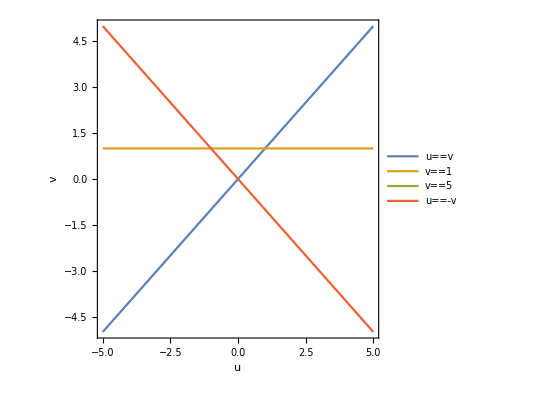

```mathematica
a1 = ContourPlot[{u==v,v==1, v==5, u == -v},{u,-5,5},{v,-5,5},Axes-> True,AxesLabel-> Automatic,PlotLegends->"Expressions"]
```

```mathematica
jac = Det[D[{x,y},{{u,v}}]]
```

-1/2

```mathematica
∫_1^5 ∫_-v^v E^((2(x+y))/(x-y))  (jac)ⅆuⅆv
```

-6 Sinh[2]